# Evolutionary Spatial Game Theory examples

Make sure this file is in the same directory as SGT.m, and then execute the following cell:

```mathematica
SetDirectory[NotebookDirectory[]];
<<SGT`
```

In any of the following examples, replace "Visualize" with "Animation" to see a movie of the result.

## Rock paper scissors

```mathematica
rps=Simulate[
InitialPopulation->Randomized[{-1,0,1},"Smoothing"->1],
Payoff->RockPaperScissors,AgentType->"Constant",
Steps->1;;100]
```

SimulationData[<100/100>]

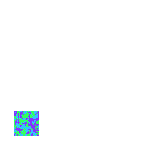
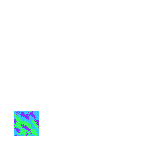
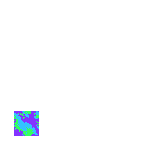
-Graphics-t = 1 | -Graphics-t = 50 | -Graphics-t = 100

```mathematica
Visualize[rps,Panels->3,Show->"Agents",ColorFunction-> PastelHue,Alignment->Vertical]
```

```mathematica
Animation[rps,Panels->3,Show->"Agents",
ColorFunction-> PastelHue,Alignment->Vertical]
```

```mathematica
ExportAnimation["rps.gif",rps,Panels->3,Show->"Agents",
ColorFunction-> PastelHue,Alignment->Vertical]
```

rps.gif

#### Smoothed initial conditions

```mathematica
rps2=Simulate[
InitialPopulation->Randomized[{-1,0,1},"Smoothing"->4],
Payoff->RockPaperScissors,AgentType->"Constant",Temperature->0.02,
Steps->1;;50]
```

SimulationData[<50/50>]

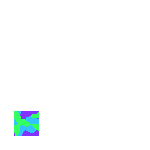
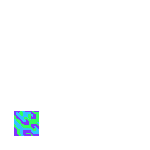
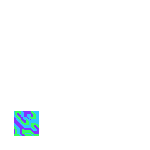
-Graphics-t = 1 | -Graphics-t = 25 | -Graphics-t = 50

```mathematica
Visualize[rps2,Panels->3,Show->"Agents",ColorFunction-> PastelHue,Alignment->Vertical]
```

```mathematica
ExportAnimation["rps2.gif",rps2,Panels->3,Show->"Agents",
ColorFunction-> PastelHue,Alignment->Vertical]
```

rps_short.gif

## Prisoner's Dilemma

### Clusters of co-operators

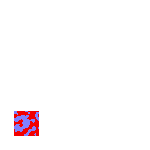
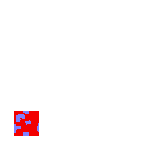
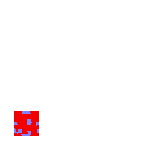
-Graphics-t = 1 | -Graphics-t = 20 | -Graphics-t = 50

```mathematica
pd1=Simulate[
InitialPopulation->Randomized[{1,1}->{-1,1}, "Smoothing"->2],
Payoff->PrisonersDilemma,AgentType->"Constant",
Neighborhood->8,Temperature->1/5];

Visualize[pd1,Panels->{1,20,50},Show->"Agents",
ColorRules->{-1->Darker[Red,0.05],0->LightBlue,1->Lighter[Blue,0.5]},
Alignment->Vertical]
```

```mathematica
ExportAnimation["pd.gif",pd1,Panels->3,Show->"Agents",
ColorRules->{-1->Darker[Red,0.05],0->LightBlue,1->Lighter[Blue,0.5]},Alignment->Vertical]
```

pd.gif

### Takeover by defectors

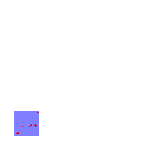
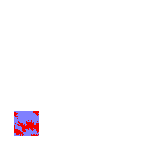
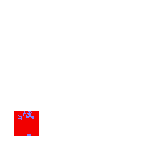
-Graphics-t = 1 | -Graphics-t = 10 | -Graphics-t = 20

```mathematica
pd2=Simulate[
InitialPopulation->Randomized[{1,2}->{-1,1}, "Smoothing"->2],
Payoff->PrisonersDilemma,AgentType->"Constant",
Neighborhood->6,Temperature->1];

Visualize[pd2,Panels->{1,10,20},Show->"Agents",
ColorRules->{-1->Darker[Red,0.05],0->LightBlue,1->Lighter[Blue,0.5]},
Alignment->Vertical]
```

```mathematica
ExportAnimation["pd2.gif",pd2,Panels->3,Show->"Agents",
ColorRules->{-1->Darker[Red,0.05],0->LightBlue,1->Lighter[Blue,0.5]},Alignment->Vertical]
```

pd2.gif

### neutral

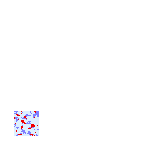
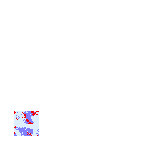
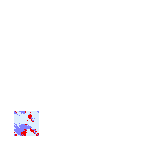
-Graphics-t = 1 | -Graphics-t = 10 | -Graphics-t = 20

```mathematica
pd3=Simulate[
InitialPopulation->Randomized[{1,2,3}->{-1,1,0}, "Smoothing"->1],
Payoff->PrisonersDilemma,AgentType->"Constant",
Neighborhood->6,Temperature->1];

Visualize[pd3,Panels->{1,10,20},Show->"Agents",
ColorRules->{-1->Darker[Red,0.05],0->LightBlue,1->Lighter[Blue,0.5]},
Alignment->Vertical]
```

```mathematica
ExportAnimation["pd3.gif",pd3,Panels->3,Show->"Agents",
ColorRules->{-1->Darker[Red,0.05],0->LightBlue,1->Lighter[Blue,0.5]},Alignment->Vertical]
```

pd3.gif

## Clustering

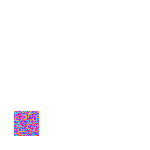
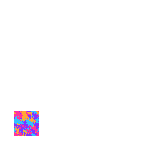
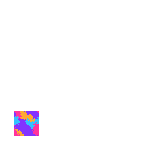
-Graphics-t = 1 | -Graphics-t = 10 | -Graphics-t = 50

```mathematica
c1=Simulate[
InitialPopulation->Randomized[{0,1,2,3}],
Payoff->Function[{x,cells}, Count[cells,x]/Length[cells]],AgentType->"Constant",
Neighborhood->6,Temperature->1];

Visualize[c1,ColorFunction->PastelHue,Panels->{1,10,50},Show->"Agents",
Alignment->Vertical]
```

```mathematica
ExportAnimation["c1.gif",c1,Panels->3,Show->"Agents",
ColorFunction-> PastelHue,Alignment->Vertical]
```

c1.gif

## Ferromagnetic Ising model

### Low temperature: spins align

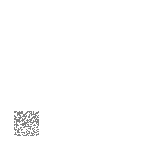
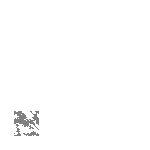
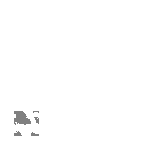
-Graphics-t = 1 | -Graphics-t = 5 | -Graphics-t = 25

```mathematica
ising1=Simulate[
InitialPopulation->Randomized[{0,1}],
Payoff->Matrix[{{1,-1},{-1,1}}],
PredictiveSelection->{0,1},
Payoff->RockPaperScissors,AgentType->"Constant",
Temperature->1/3];

Visualize[ising1,Panels->{1,5,25},Show->"Agents",
ColorRules->{0->White,1->Gray}]
```

```mathematica
ExportAnimation["ising.gif",ising1,Show->"Agents",
ColorRules->{0->White,1->Gray}]
```

ising.gif

### High temperature: thermal fluctuations prevent domains

```mathematica
ising2=Simulate[
InitialPopulation->Randomized[{0,1}],
Payoff->Matrix[{{1,-1},{-1,1}}],
PredictiveSelection->{0,1},
Payoff->RockPaperScissors,AgentType->"Constant",
Temperature->1];

Visualize[ising2,Panels->{1,5,25},Show->"Actions",
Alignment->Vertical]
```

-Graphics-t = 1 | -Graphics-t = 5 | -Graphics-t = 25

```mathematica
ExportAnimation["ising2.gif",ising2,Panels->3,Show->"Actions",
Alignment->Vertical]
```

ising2.gif

## Evolution

### Iterated prisoners dilemma in which the players play probabilistically (bright red is always defect, bright green is always cooperate), and in which occasional mutations in the probability can occur

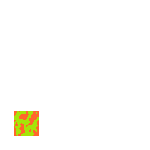
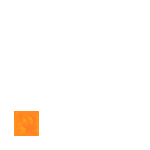
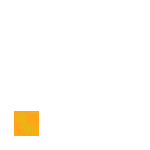
-Graphics-t = 1 | -Graphics-t = 100 | -Graphics-t = 500

```mathematica
evo=Simulate[
InitialPopulation->Randomized[
{_->Poisson[0.15], _-> Poisson[0.85]},"Smoothing"->2],
Payoff->Matrix[{{-2,4},{-4,2}}],
Actions->{0,1},AgentType->"Complex",
Steps->1;;500,Temperature->1/5,
MutationRate->0.005];

Visualize[evo,Panels->{1,100,500},ColorUsing->Function[AgentTable[#]⟦2,1⟧],
ColorFunction->RedGreen,Show->"Agents"]
```

```mathematica
ExportAnimation["evo.gif",evo,ColorUsing->Function[AgentTable[#]⟦2,1⟧],
ColorFunction->RedGreen,Show->"Agents","Every"->3,"Limit"->250]
```

evo2.gif